```mathematica
F[x_]=3 x^4-16 x^3+24x; (*задана функція*)
```

```mathematica
A=3.; (*початок відрізку пошуку*) 
B=4.; (*кінець відрізку пошуку*)

ϵ=0.001;      (*точність*)
```

```mathematica
result={};
```

```mathematica
min=Minimize[F[x], A<x<B, x] (*знаходження мінімума функції*)
```

{-161.568,{x→3.8662}}

```mathematica
(*Графік функції*)
```

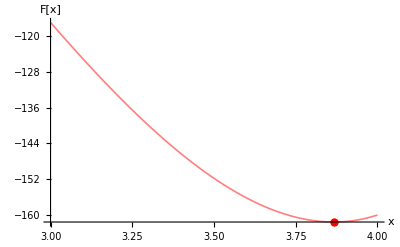

```mathematica
Plot[F[x], {x, A, B}, PlotRange->All, PlotStyle-> {Pink,Thickness[0.003]}, AxesLabel->{x, "F[x]"}, Epilog->{Red, PointSize[0.015], Point[{min[[2,1,2]], min[[1]] }]}]
```

```mathematica
(*Метод золотого перерізу*)
```

```mathematica
τ= N[Solve[x^2-x-1== 0, x][[2,1,2]]]; (*обчислюємо параметр τ*)
```

```mathematica
(*1 ітерація*)
kk=0;
ak= A;
bk=B;
x12k= ak + (bk-ak)/τ^2; (*значення аргументу*)
x22k= ak + (bk-ak)/τ;(*значення аргументу*)
Fx10=F[x12k];
Fx20=F[x22k];
ab={}; (*масив значень кінців відрізка*)
Fx2={ }; (*масив значень функції Fxk *)
xx = {}; (*масив значень аргументу xk*)
AppendTo[ab, {ak, bk}];
AppendTo[xx, {x12k, x22k}];
AppendTo[Fx2, {Fx10, Fx20}];
res2={};
AppendTo[res2,{0,x12k,x22k,Fx2[[-1,1]],Fx2[[-1,2]],Abs[bk-ak]}];
If[Fx2[[kk+1,1]]≥ Fx2[[kk+1,2]], 
{ak = xx[[kk+1,1]];
bk = ab[[kk+1,2]];
AppendTo[ab, {ak, bk}];
x12k = xx[[kk+1, 2]];
Fx10= Fx2[[kk+1,2]];
x22k = ak + (bk-ak)/τ;
AppendTo[xx, {x12k, x22k}];
Fx20= F[xx[[kk+2, 2]]];
AppendTo[Fx2, {Fx10, Fx20}];}, 
{ak=ab[[kk+1, 1]];
bk = xx[[kk+1,2]];
AppendTo[ab, {ak, bk}];
x22k = xx[[kk+1, 1]];
Fx20= Fx2[[kk+1, 1]] ;
x12k = ak + (bk-ak)/τ^2;
AppendTo[xx, {x12k, x22k}];
Fx10= F[xx[[kk+2, 1]]];
AppendTo[Fx2, {Fx10, Fx20}];}]
AppendTo[res2,{1,x12k,x22k,Fx2[[-1,1]],Fx2[[-1,2]],Abs[bk-ak]}];
If[Abs[ab[[kk+2,2]]-ab[[kk+2,1]]] ≤  ϵ,  Break[]];
(*цикл методу*)
t1=AbsoluteTime[]; (*початок роботи методу*)
For[kk = 1, kk < 100000, kk++,
{If[Fx2[[kk+1,1]]≥ Fx2[[kk+1,2]], {ak = xx[[kk+1,1]];
bk = ab[[kk+1,2]];
AppendTo[ab, {ak, bk}];
x12k = xx[[kk+1, 2]];
Fx10= Fx2[[kk+1,2]];
x22k = ak + (bk-ak)/τ;
AppendTo[xx, {x12k, x22k}];
Fx20= F[xx[[kk+2, 2]]];
AppendTo[Fx2, {Fx10, Fx20}]}, {ak=ab[[kk+1, 1]];
bk = xx[[kk+1,2]];
AppendTo[ab, {ak, bk}];
x22k = xx[[kk+1, 1]];
Fx20= Fx2[[kk+1, 1]] ;
x12k = ak + (bk-ak)/τ^2;
AppendTo[xx, {x12k, x22k}];
Fx10= F[xx[[kk+2, 1]]];
AppendTo[Fx2, {Fx10, Fx20}]}];
AppendTo[res2,{kk+1,x12k,x22k,Fx2[[-1,1]],Fx2[[-1,2]],Abs[ab[[kk+2,2]]-ab[[kk+2,1]]]}];
If[Abs[ab[[kk+2,2]]-ab[[kk+2,1]]] ≤  ϵ,  Break[]];
If[kk > 100, Break[]]}]
t2=AbsoluteTime[]; (*кінець роботи методу*)
Grid[Prepend[res2,{"k","x_1^(k)","x_2^(k)","F[x_1^(k)]"," F[x_2^(k)]","Abs[b-a]"}]]
Print["Час роботи циклу\t",t=t2-t1,"\nОтримане наближення\t",xs1= (ab[[-1,1]]+ab[[-1,2]])/2,"\nЗначення функції\t", F[(ab[[-1,1]]+ab[[-1,2]])/2],"\nДовжина інтервалу невизначеності\t", Abs[bk-ak]];
A2=Abs[xs1-c];

AppendTo[result,{kk+2,ab[[-1,1]],ab[[-1,2]],Abs[bk-ak],A2,t,kk+3,xs1,F[xs1]}];
```

{Null}

k | x_1^(k) | x_2^(k) | F[x_1^(k)] |  F[x_2^(k)] | Abs[b-a]
0 | 3.38197 | 3.61803 | -145.281 | -156.88 | 1.
1 | 3.61803 | 3.76393 | -156.88 | -160.727 | 0.618034
2 | 3.76393 | 3.8541 | -160.727 | -161.556 | 0.381966
3 | 3.8541 | 3.90983 | -161.556 | -161.407 | 0.236068
4 | 3.81966 | 3.8541 | -161.391 | -161.556 | 0.145898
5 | 3.8541 | 3.87539 | -161.556 | -161.561 | 0.0901699
6 | 3.87539 | 3.88854 | -161.561 | -161.526 | 0.0557281
7 | 3.86726 | 3.87539 | -161.568 | -161.561 | 0.0344419
8 | 3.86223 | 3.86726 | -161.567 | -161.568 | 0.0212862
9 | 3.86726 | 3.87036 | -161.568 | -161.567 | 0.0131556
10 | 3.86534 | 3.86726 | -161.568 | -161.568 | 0.00813062
11 | 3.86415 | 3.86534 | -161.568 | -161.568 | 0.005025
12 | 3.86534 | 3.86607 | -161.568 | -161.568 | 0.00310562
13 | 3.86607 | 3.86652 | -161.568 | -161.568 | 0.00191938
14 | 3.86579 | 3.86607 | -161.568 | -161.568 | 0.00118624
15 | 3.86607 | 3.86624 | -161.568 | -161.568 | 0.000733137

Час роботи циклу	0.001071
Отримане наближення	3.86616
Значення функції	-161.568
Довжина інтервалу невизначеності	0.000733137